```mathematica
trainingset=Import ["https://raw.githubusercontent.com/zhu-research-group/auto_qsar_cl_transport/refs/tags/v1/ChlorideTransporters-TrainingSet-1.sdf","Metadata"]
```

{<|SMILES→CC(CC(C#N)(C1=CC=CC=C1)C2=CC=CC=C2)N3CCCCC3,NSC#→NSC13176,Activity→1|>,<|SMILES→C1=CC(=CC=C1C2=NC3=C(N=C(N=C3N=C2C4=CC=C(C=C4)N)N)N)N,NSC#→NSC61642,Activity→1|>,<|SMILES→CCN(CC)CCN1C2=CC=CC=C2SC3=C1C4=CC=CC=C4C=C3,NSC#→NSC18883,Activity→1|>,<|SMILES→CC(C)(C)NC(=S)NC(C)(C)C,NSC#→NSC47496,Activity→1|>,<|SMILES→CC1=COC(CC1)(C)C=NCC(=C)C,NSC#→NSC40817,Activity→1|>,<|SMILES→CC1=C(C=C(C=C1)C(C)C)NC(=O)NC2=CC=C(C=C2)[N+](=O)[O-],NSC#→NSC46492,Activity→1|>,<|SMILES→CCCN1C=C2CC3C(C4=C2C1=CC=C4)CC(C)CN3C,NSC#→NSC332294,Activity→1|>,<|SMILES→COC1=CC=CC=C1NC(=O)C2=CC3=CC=CC=C3C=C2O,NSC#→NSC50680,Activity→1|>,<|SMILES→C1=CC=C(C=C1)C2=C(OC(=N2)C3=NC=CC4=CC=CC=C43)C5=CC=CC=C5,NSC#→NSC25457,Activity→1|>,<|SMILES→CC1=CC(=C(C=C1NC2=C3C=C(C=CC3=NC4=C2C=CC(=C4)Cl)OC)C(C)C)O,NSC#→NSC13051,Activity→1|>,<|SMILES→CCOC1=CC=C(C=C1)NC(=O)C2=CC3=CC=CC=C3C=C2O,NSC#→NSC50690,Activity→1|>,<|SMILES→CCC(C1C(CC(O1)(CC)C2CCC(C(O2)C)(CC)O)C)C(=O)C(C)C(C(C)CCC3=C(C(=C(C=C3)C)O)C(=O)O)O,NSC#→NSC177406,Activity→1|>,<|SMILES→CC1=CC=C(C=C1)N2CCN(CC2)CC(COC3=CC=CC(=C3)C)O,NSC#→NSC91382,Activity→1|>,<|SMILES→CC(C)(C)N1C(=CC(=N1)C2CC2)NC(=O)NC3=CC=CC=C3,NSC#→NSC366802,Activity→1|>,<|SMILES→C1=CC=C(C(=C1)NC(=O)NC2=CC=C(C=C2)Br)Cl,NSC#→NSC190501,Activity→1|>,<|SMILES→CCCCCC1=C(NC(=C1)C=C2C(=CC(=N2)C3=CC=CN3)OC)C,NSC#→NSC47147,Activity→1|>,<|SMILES→C1=CC=C(C(=C1)C(=O)N)OCC(=O)NC2=CC(=C(C=C2)Cl)Cl,NSC#→NSC33738,Activity→1|>,<|SMILES→C=CCNC(=S)NC1=CC=C(C=C1)OC(=O)NC2=CC(=C(C=C2)Cl)Cl,NSC#→NSC204262,Activity→1|>,<|SMILES→C#CC1=CC(=CC=C1)NC(=O)C2=C(C=C(C=C2)Cl)Cl,NSC#→NSC372769,Activity→1|>,<|SMILES→CC1CC2=C(C(=CC(=C2C(N1)C)O)O)C3=CC(=C(C4=C3C=C(C=C4OC)C)O)C5=C(C6=C(C=C(C=C6OC)C)C(=C5)C7=C8CC(NC(C8=C(C=C7O)O)C)C)O,NSC#→NSC661755,Activity→1|>,<|SMILES→CC1=CC=C(C=C1)N=NC2=CC=C(C(=O)C=C2)OC(=O)C(=C)C,NSC#→NSC79559,Activity→1|>,<|SMILES→CC1CCC(OC1C(C)C(=O)O)CC2CC(C(C3(O2)C(CC(O3)(C)C4CCC(O4)(C)C5C(CC(O5)C6C(CC(C(O6)(CO)O)C)C)C)C)C)OC,NSC#→NSC292567,Activity→1|>,<|SMILES→COC1=CC(=C(C=C1NC(=O)C2=CC3=CC=CC=C3C=C2O)OC)Cl,NSC#→NSC50688,Activity→1|>,<|SMILES→C1=CC=C(C(=C1)NC(=O)NC2=CC(=C(C=C2)Cl)Cl)O,NSC#→NSC522131,Activity→1|>,<|SMILES→C1=CC=C2C(=C1)C=CC(=N2)C=CC(=O)C3=C(C=CC(=C3)Cl)O,NSC#→NSC71097,Activity→1|>,<|SMILES→CC1=NC(=CC=C1)NC(=S)NC2=CC=CC(=N2)C,NSC#→NSC20618,Activity→1|>,<|SMILES→C1=CNC(=O)C(=C1)OC(=O)NC2=CC=C(C=C2)F,NSC#→NSC282187,Activity→1|>,<|SMILES→C1C2CC3C1C3C2=NN=C4C5CC6C4C6C5,NSC#→NSC122987,Activity→1|>,<|SMILES→C1=CC=C2C=C(C(=CC2=C1)C(=O)NC3=CC(=CC=C3)[N+](=O)[O-])O,NSC#→NSC37168,Activity→1|>,<|SMILES→C1=CC=C2C(=C1)C3=CC(=C(C=C3N2)O)C(=O)NC4=CC=C(C=C4)Cl,NSC#→NSC50651,Activity→1|>,<|SMILES→CCCCCC1=C2C(=CC(=C1)O)OC(=O)C3=C(C=C(C=C3O2)O)C(=O)CCCC,NSC#→NSC31867,Activity→1|>,<|SMILES→CCCC(=CC1=NC=C(C=C1)CC)C,NSC#→NSC63314,Activity→1|>,<|SMILES→CC(=CCC1=C2C(=C(C3=C1OC(C=C3)(C)C)OC)C(=C(C(=O)O2)C4=CC=C(C=C4)O)O)C,NSC#→NSC307981,Activity→1|>,<|SMILES→C1=CC=C2C(=C1)C=C(N2)C=C[N+](=O)[O-],NSC#→NSC150982,Activity→1|>,<|SMILES→C1CCC(=NNC2=NC3=CC=CC=C3C=C2)CC1,NSC#→NSC118723,Activity→1|>,<|SMILES→C1CC(OC=C1)COC(=O)C2CCC=CO2,NSC#→NSC38983,Activity→1|>,<|SMILES→CN1CCN(C2CC3=CC=CC=C3SC4=C2C=C(SC)C=C4)CC1,NSC#→NSC281816,Activity→1|>,<|SMILES→CC1=C(C=C(C=C1)[N+](=O)[O-])NC(=O)NC2=CC(=CC=C2)F,NSC#→NSC216183,Activity→1|>,<|SMILES→CC1=CC2=C(C=C1)NCCC2=C(C#N)C#N,NSC#→NSC108753,Activity→1|>,<|SMILES→CC1C=CC=C(C(=O)NC2=C(C(=C3C(=C2O)C(=C(C4=C3C(=O)C(O4)(OC=CC(C(C(C(C(C(C1O)C)O)C)OC(=O)C)C)OC)C)C)O)O)CN(C)C)C,NSC#→NSC145612,Activity→1|>,<|SMILES→CC(C)(C)C1=CC(=CC(=C1O)C(C)(C)C)C=C(C#N)C#N,NSC#→NSC242557,Activity→1|>,<|SMILES→C1=COC(=C1)CNC(=O)NC2=CC=C(C=C2)[N+](=O)[O-],NSC#→NSC45086,Activity→1|>,<|SMILES→C1=CC=C(C=C1)C(C2=CC=CC=C2)(C3=NC=CN3C4=CC=CC=C4)O,NSC#→NSC40269,Activity→1|>,<|SMILES→CC1=CC=C(N1)C(=O)OC2C(C(OC(C2OC)(C)C)OC3=C(C4=C(C=C3)C(=C(C(=O)O4)NC(=O)C5=CC(=C(C=C5)O)CC=C(C)C)O)Cl)O,NSC#→NSC227186,Activity→1|>,<|SMILES→CC1=C(N=C(N1)N=NC2=CC=CC=C2)N=NC3=CC=CC=C3,NSC#→NSC40749,Activity→1|>,<|SMILES→C1CCC2(CC1)C(=S)NC3(N2)CCCCC3,NSC#→NSC515893,Activity→1|>,<|SMILES→C=CCNC(=S)NC1=CC(=CC=C1)[N+](=O)[O-],NSC#→NSC102086,Activity→1|>,<|SMILES→CC1=CC=CC=C1N2CCN(CC2)C(=S)C3=CC=C(C=C3)OC,NSC#→NSC83497,Activity→1|>,<|SMILES→C1=CC=C(C(=C1)N=NC2=C(N=C(C=C2)N)N)Cl,NSC#→NSC106208,Activity→1|>,<|SMILES→CCC(CNC1=C2C(=CC(=C1)OC)C=CC=N2)NC3CCCCC3,NSC#→NSC13616,Activity→1|>,<|SMILES→CC1=CC(=NC=C1)NC(C2=CC=CC=C2)C3=C(C4=C(C=CC=N4)C=C3)O,NSC#→NSC1014,Activity→1|>,<|SMILES→CCOC1=CC=C(C=C1)NC(=O)NC2=C(C=CC(=C2)C(C)C)C,NSC#→NSC46213,Activity→1|>,<|SMILES→C1=CC(=CC=C1NC(=O)NC2=CC=C(C=C2)OC3=CC=C(C=C3)NC(=O)NC4=CC=C(C=C4)[N+](=O)[O-])[N+](=O)[O-],NSC#→NSC80735,Activity→1|>,<|SMILES→C1=CC=C2C(=C1)C=CC(=C2O)C(=O)NC3=CC(=CC=C3)[N+](=O)[O-],NSC#→NSC50648,Activity→1|>,<|SMILES→C1=CC=C2C=C(C=CC2=C1)C=C3C(=O)NC(=O)NC3=O,NSC#→NSC95909,Activity→0|>,<|SMILES→C1CC[N+]2(C(C1)CCCC2CO)[O-],NSC#→NSC34552,Activity→0|>,<|SMILES→C1=CN(C=C1)CCC2=CC=NC=C2,NSC#→NSC42774,Activity→0|>,<|SMILES→C1CCC(CC1)N2CC2CO,NSC#→NSC44680,Activity→0|>,<|SMILES→COC1=CC=C(C=C1)N=NC2=C(N=C(C=C2)N)N,NSC#→NSC78130,Activity→0|>,<|SMILES→CC1CC(C(C(C=C(C(C(C=CC=C(C(=O)NC2=CC(=CC(=C2O)C1OC)O)C)C)OC(=O)N)C)C)OC)OC,NSC#→NSC330500,Activity→0|>,<|SMILES→C1C2C=C(C(N1CC3=CC=CC=C3)C4C2C(=O)N(C4=O)C5=CC=CC=C5)C#N,NSC#→NSC118818,Activity→0|>,<|SMILES→CC1CC(CC(C1=O)C(CC2CC(=O)NC(=O)C2)O)(C)OC(=O)C,NSC#→NSC32743,Activity→0|>,<|SMILES→C1CC(OC1)N2C=NC3=C2NC=NC3=S,NSC#→NSC45153,Activity→0|>,<|SMILES→CCSC1=NC(=S)C=C(N1)C,NSC#→NSC67307,Activity→0|>,<|SMILES→CC1=CC2=C(C=C1C)N(CC(=O)N2)C(=O)CCl,NSC#→NSC138389,Activity→0|>,<|SMILES→CC1=C2C(C(=O)C3(C(CC4C(C3C(C(C2(C)C)(CC1O)O)OC(=O)C5=CC=CC=C5)(CO4)OC(=O)C)O)C)OC(=O)C,NSC#→NSC330753,Activity→0|>,<|SMILES→C1CN(CCN1CC(COC2=CC=CC3=CC=CC=C32)O)C4=CC=CC=C4Cl,NSC#→NSC91396,Activity→0|>,<|SMILES→C1=CC=C(C(=C1)C2=NNC(=O)NC2=O)N3C(=O)NC(=O)C(=N3)C(=O)O,NSC#→NSC362639,Activity→0|>,<|SMILES→C1=CC(=CC=C1C(=O)NC2=CC=C(C=C2)NC3=CC=NC=C3)N,NSC#→NSC146770,Activity→0|>,<|SMILES→C1=CC=C(C(=C1)NC2=CC(=NC(=N2)N)Cl)Cl,NSC#→NSC47522,Activity→0|>,<|SMILES→CC1=C(C=CC=C1Cl)NC2=C(C=CC=N2)C(=O)OCC(CO)O,NSC#→NSC335504,Activity→0|>,<|SMILES→CCC1=C2C3=C(C=C(C=C3)[N+](=O)[O-])NC2=CC=C1,NSC#→NSC9852,Activity→0|>,<|SMILES→C1C2=C(C=C(C=C2)N)N=[N+](C3=C1C=CC(=C3)N)[O-],NSC#→NSC70534,Activity→0|>,<|SMILES→C1=C(C=C(C(=C1S(=O)(=O)N)N)Cl)S(=O)(=O)N,NSC#→NSC17148,Activity→0|>,<|SMILES→CCCCN1C(=O)CC2C1(OCC2)C,NSC#→NSC134785,Activity→0|>,<|SMILES→CCOC1=CC=C(C2=[N+](ON=C12)[O-])S(=O)(=O)C3=CC=C(C=C3)C,NSC#→NSC228137,Activity→0|>,<|SMILES→CC1=C(N=CC=C1)NC(=O)C2=CSN=N2,NSC#→NSC120286,Activity→0|>,<|SMILES→CC1=CN(C(=O)N(C1=O)CC2=CC=CC=C2)C3CC(C(O3)CO)O,NSC#→NSC106464,Activity→0|>,<|SMILES→CC1=C(C(=O)C2=C(C1=O)N3CC4C(C3(C2COC(=O)N)OC)N4)N,NSC#→NSC26980,Activity→0|>,<|SMILES→CSC1=NC(=CC(=O)N1)Cl,NSC#→NSC45719,Activity→0|>,<|SMILES→CC(CN1CCOCC1)OC(=O)C2=CC(=C(C(=C2)OC)OC)OC,NSC#→NSC169409,Activity→0|>,<|SMILES→C1=CC=C(C=C1)C=C(C2=CC=CC=C2)C(=O)O,NSC#→NSC40614,Activity→0|>,<|SMILES→C1=CC(=C(C=C1[As](=O)(C2=CC(=C(C=C2)O)[N+](=O)[O-])O)[N+](=O)[O-])O,NSC#→NSC49852,Activity→0|>,<|SMILES→C1=CC2=C(C=C1Cl)SC(=S)N2,NSC#→NSC503425,Activity→0|>,<|SMILES→CC(=O)OC1CCC2(C(C1(C)C)CC(C3=CC(CCC2=O)C(=C)C3=O)O)C,NSC#→NSC302979,Activity→0|>,<|SMILES→CC1CC(C(C(C=C(C(C(C=CC=C(C(=O)NC2=C(C(=O)C(=C(C1)C2=O)OC)C=NN3CCOCC3)C)OC)OC(=O)N)C)C)O)OC,NSC#→NSC255112,Activity→0|>,<|SMILES→COC1=CC2=C(C=C1)C3COC4=C(C3O2)C=CC(=C4)O,NSC#→NSC350085,Activity→0|>,<|SMILES→C1CC(=O)N(C(=O)C1)C2=C(C=C(C=C2)[N+](=O)[O-])N,NSC#→NSC660300,Activity→0|>,<|SMILES→COC1=CC=CC(=C1OC)C=CC2=NC=CC3=CC=CC=C32,NSC#→NSC164880,Activity→0|>,<|SMILES→COC1=C(C=C(C(=C1)CC(=O)C2=CNC3=CC=CC=C32)Cl)OC,NSC#→NSC105348,Activity→0|>,<|SMILES→C1C(OC(=S)N1)COC2=CC=CC(=C2)C(F)(F)F,NSC#→NSC97865,Activity→0|>,<|SMILES→CC1=C(C2=C(C=C1)C=CC(=C2)C#N)O,NSC#→NSC128068,Activity→0|>,<|SMILES→CC1=C(C(=CC=C1)Cl)N=C2N(C3(CCCCC3)C(=C)S2)C(=O)C4=C(C5=CC=CC=C5S4)Cl,NSC#→NSC310325,Activity→0|>,<|SMILES→CC(=O)C1CCCC(=O)C=CC(=O)O1,NSC#→NSC180515,Activity→0|>,<|SMILES→C1COCCN1C(=O)COC2=C(C=C(C=C2)[N+](=O)[O-])Cl,NSC#→NSC145992,Activity→0|>,<|SMILES→C1=CC(=CC(=C1)[N+](=O)[O-])C2=C(N3C=CC=NC3=N2)N=O,NSC#→NSC369066,Activity→0|>,<|SMILES→CN1C2=NC=NC(=C2CC3=CC=CC=C3C1=O)NCC4=CC=CC=C4,NSC#→NSC295300,Activity→0|>,<|SMILES→C1=CC(=CC=C1N)N=C(C(=NC2=CC=C(C=C2)N)N)N,NSC#→NSC175743,Activity→0|>,<|SMILES→C1=CC=C(C(=C1)NC(=O)NC2=CC=C(C=C2)SCC(=O)O)F,NSC#→NSC142277,Activity→0|>,<|SMILES→C1=CC=C(C=C1)C2=C(N=CN2)C3=CC=CC=C3,NSC#→NSC59776,Activity→0|>,<|SMILES→CN1C2=NC(=CN=C2C(=N1)NC(=O)C(F)(F)F)C3=CC=C(C=C3)Cl,NSC#→NSC163823,Activity→0|>,<|SMILES→C1=CC=C(C(=C1)NC2=CC=CC=N2)O,NSC#→NSC50751,Activity→0|>,<|SMILES→CC1=NN(C(=O)C1N=NC2=CC=C(C=C2)S(=O)(=O)N)C3=CC=CC=C3,NSC#→NSC114414,Activity→0|>,<|SMILES→CC1CCC2C(C1)NCCN2,NSC#→NSC28011,Activity→0|>,<|SMILES→C1=CC2=CC(=C3C=CC=NC3=C2N=C1)[N+](=O)[O-],NSC#→NSC4263,Activity→0|>,<|SMILES→CC1C(OC(=O)CC(CC(CC(CCC(C(CC(=O)CC(C(C(CC(C=CC=CC=CC=CCCC=CC=CC(C1O)(C)O)OC2C(C(C(C(O2)C)O)N)O)O)C(=O)O)O)O)O)O)O)O)C,NSC#→NSC150817,Activity→0|>,<|SMILES→CC1=C(C(=O)C=C2C1=CC=C3C2(CCC4(C3(CCC5(C4CC(CC5)(C)C(=O)O)C)C)C)C)O,NSC#→NSC70931,Activity→0|>,<|SMILES→C1=CC(=CC=C1C(=O)N)OC2=CC=C(C=C2)C(=O)N,NSC#→NSC39047,Activity→0|>,<|SMILES→CC1=C(OC2=C1C(=O)NCCC2)[N+](=O)[O-],NSC#→NSC290307,Activity→0|>,<|SMILES→CC1C(C(=O)C2(O1)CC3C(C2OC(=O)C)(CC45N3C(=O)C(N(C4=O)C)(SS5)CO)O)(C)C,NSC#→NSC294408,Activity→0|>,<|SMILES→C1=CC(=CC=C1NC2=NC=CC(=O)N2)Cl,NSC#→NSC23672,Activity→0|>,<|SMILES→CC1(CSC(=N1)NC2=CC=C(C=C2)OC)CO,NSC#→NSC319471,Activity→0|>,<|SMILES→CCC(C)NC(=O)C1=CC=CC(=C1)C,NSC#→NSC34983,Activity→0|>,<|SMILES→CN1CCN(CC1)C(=O)NC2=CC=C(C=C2)[N+](=O)[O-],NSC#→NSC36815,Activity→0|>,<|SMILES→C1CNC2CCNC3N2C1NCC3,NSC#→NSC81462,Activity→0|>,<|SMILES→CCOC1=CC=C(C=C1)NC(=O)C2CCCN(C2)C,NSC#→NSC22806,Activity→0|>,<|SMILES→C1=CC(=CN=C1)[As](=O)(O)O,NSC#→NSC31741,Activity→0|>,<|SMILES→CC1=C2C3=C(C4=C(C=C3)C(=O)C=CC4=O)N(C2=CC=C1)C,NSC#→NSC645330,Activity→0|>,<|SMILES→CC1=CC=CC=C1NC(=O)NCCN2CC2,NSC#→NSC101266,Activity→0|>,<|SMILES→C1CSC(=S)N1CCO,NSC#→NSC29629,Activity→0|>,<|SMILES→CC(C)(C)N1CCC1CN,NSC#→NSC135857,Activity→0|>,<|SMILES→CC1COC2C3C4C1CCC4CC5C3C(C6=C2C(=O)C=CC6=O)OC5=O,NSC#→NSC401005,Activity→0|>,<|SMILES→CCOC(=O)C1CC(=C(CC1C(=O)O)C)C,NSC#→NSC144982,Activity→0|>}

```mathematica
Length[trainingset]
data=trainingset[[1]]
data[["SMILES"]]
```

123

<|SMILES→CC(CC(C#N)(C1=CC=CC=C1)C2=CC=CC=C2)N3CCCCC3,NSC#→NSC13176,Activity→1|>

CC(CC(C#N)(C1=CC=CC=C1)C2=CC=CC=C2)N3CCCCC3

```mathematica
smilesdata=Table[trainingset[[i,"SMILES"]],{i,Length[trainingset]}]
```

{CC(CC(C#N)(C1=CC=CC=C1)C2=CC=CC=C2)N3CCCCC3,C1=CC(=CC=C1C2=NC3=C(N=C(N=C3N=C2C4=CC=C(C=C4)N)N)N)N,CCN(CC)CCN1C2=CC=CC=C2SC3=C1C4=CC=CC=C4C=C3,CC(C)(C)NC(=S)NC(C)(C)C,CC1=COC(CC1)(C)C=NCC(=C)C,CC1=C(C=C(C=C1)C(C)C)NC(=O)NC2=CC=C(C=C2)[N+](=O)[O-],CCCN1C=C2CC3C(C4=C2C1=CC=C4)CC(C)CN3C,COC1=CC=CC=C1NC(=O)C2=CC3=CC=CC=C3C=C2O,C1=CC=C(C=C1)C2=C(OC(=N2)C3=NC=CC4=CC=CC=C43)C5=CC=CC=C5,CC1=CC(=C(C=C1NC2=C3C=C(C=CC3=NC4=C2C=CC(=C4)Cl)OC)C(C)C)O,CCOC1=CC=C(C=C1)NC(=O)C2=CC3=CC=CC=C3C=C2O,CCC(C1C(CC(O1)(CC)C2CCC(C(O2)C)(CC)O)C)C(=O)C(C)C(C(C)CCC3=C(C(=C(C=C3)C)O)C(=O)O)O,CC1=CC=C(C=C1)N2CCN(CC2)CC(COC3=CC=CC(=C3)C)O,CC(C)(C)N1C(=CC(=N1)C2CC2)NC(=O)NC3=CC=CC=C3,C1=CC=C(C(=C1)NC(=O)NC2=CC=C(C=C2)Br)Cl,CCCCCC1=C(NC(=C1)C=C2C(=CC(=N2)C3=CC=CN3)OC)C,C1=CC=C(C(=C1)C(=O)N)OCC(=O)NC2=CC(=C(C=C2)Cl)Cl,C=CCNC(=S)NC1=CC=C(C=C1)OC(=O)NC2=CC(=C(C=C2)Cl)Cl,C#CC1=CC(=CC=C1)NC(=O)C2=C(C=C(C=C2)Cl)Cl,CC1CC2=C(C(=CC(=C2C(N1)C)O)O)C3=CC(=C(C4=C3C=C(C=C4OC)C)O)C5=C(C6=C(C=C(C=C6OC)C)C(=C5)C7=C8CC(NC(C8=C(C=C7O)O)C)C)O,CC1=CC=C(C=C1)N=NC2=CC=C(C(=O)C=C2)OC(=O)C(=C)C,CC1CCC(OC1C(C)C(=O)O)CC2CC(C(C3(O2)C(CC(O3)(C)C4CCC(O4)(C)C5C(CC(O5)C6C(CC(C(O6)(CO)O)C)C)C)C)C)OC,COC1=CC(=C(C=C1NC(=O)C2=CC3=CC=CC=C3C=C2O)OC)Cl,C1=CC=C(C(=C1)NC(=O)NC2=CC(=C(C=C2)Cl)Cl)O,C1=CC=C2C(=C1)C=CC(=N2)C=CC(=O)C3=C(C=CC(=C3)Cl)O,CC1=NC(=CC=C1)NC(=S)NC2=CC=CC(=N2)C,C1=CNC(=O)C(=C1)OC(=O)NC2=CC=C(C=C2)F,C1C2CC3C1C3C2=NN=C4C5CC6C4C6C5,C1=CC=C2C=C(C(=CC2=C1)C(=O)NC3=CC(=CC=C3)[N+](=O)[O-])O,C1=CC=C2C(=C1)C3=CC(=C(C=C3N2)O)C(=O)NC4=CC=C(C=C4)Cl,CCCCCC1=C2C(=CC(=C1)O)OC(=O)C3=C(C=C(C=C3O2)O)C(=O)CCCC,CCCC(=CC1=NC=C(C=C1)CC)C,CC(=CCC1=C2C(=C(C3=C1OC(C=C3)(C)C)OC)C(=C(C(=O)O2)C4=CC=C(C=C4)O)O)C,C1=CC=C2C(=C1)C=C(N2)C=C[N+](=O)[O-],C1CCC(=NNC2=NC3=CC=CC=C3C=C2)CC1,C1CC(OC=C1)COC(=O)C2CCC=CO2,CN1CCN(C2CC3=CC=CC=C3SC4=C2C=C(SC)C=C4)CC1,CC1=C(C=C(C=C1)[N+](=O)[O-])NC(=O)NC2=CC(=CC=C2)F,CC1=CC2=C(C=C1)NCCC2=C(C#N)C#N,CC1C=CC=C(C(=O)NC2=C(C(=C3C(=C2O)C(=C(C4=C3C(=O)C(O4)(OC=CC(C(C(C(C(C(C1O)C)O)C)OC(=O)C)C)OC)C)C)O)O)CN(C)C)C,CC(C)(C)C1=CC(=CC(=C1O)C(C)(C)C)C=C(C#N)C#N,C1=COC(=C1)CNC(=O)NC2=CC=C(C=C2)[N+](=O)[O-],C1=CC=C(C=C1)C(C2=CC=CC=C2)(C3=NC=CN3C4=CC=CC=C4)O,CC1=CC=C(N1)C(=O)OC2C(C(OC(C2OC)(C)C)OC3=C(C4=C(C=C3)C(=C(C(=O)O4)NC(=O)C5=CC(=C(C=C5)O)CC=C(C)C)O)Cl)O,CC1=C(N=C(N1)N=NC2=CC=CC=C2)N=NC3=CC=CC=C3,C1CCC2(CC1)C(=S)NC3(N2)CCCCC3,C=CCNC(=S)NC1=CC(=CC=C1)[N+](=O)[O-],CC1=CC=CC=C1N2CCN(CC2)C(=S)C3=CC=C(C=C3)OC,C1=CC=C(C(=C1)N=NC2=C(N=C(C=C2)N)N)Cl,CCC(CNC1=C2C(=CC(=C1)OC)C=CC=N2)NC3CCCCC3,CC1=CC(=NC=C1)NC(C2=CC=CC=C2)C3=C(C4=C(C=CC=N4)C=C3)O,CCOC1=CC=C(C=C1)NC(=O)NC2=C(C=CC(=C2)C(C)C)C,C1=CC(=CC=C1NC(=O)NC2=CC=C(C=C2)OC3=CC=C(C=C3)NC(=O)NC4=CC=C(C=C4)[N+](=O)[O-])[N+](=O)[O-],C1=CC=C2C(=C1)C=CC(=C2O)C(=O)NC3=CC(=CC=C3)[N+](=O)[O-],C1=CC=C2C=C(C=CC2=C1)C=C3C(=O)NC(=O)NC3=O,C1CC[N+]2(C(C1)CCCC2CO)[O-],C1=CN(C=C1)CCC2=CC=NC=C2,C1CCC(CC1)N2CC2CO,COC1=CC=C(C=C1)N=NC2=C(N=C(C=C2)N)N,CC1CC(C(C(C=C(C(C(C=CC=C(C(=O)NC2=CC(=CC(=C2O)C1OC)O)C)C)OC(=O)N)C)C)OC)OC,C1C2C=C(C(N1CC3=CC=CC=C3)C4C2C(=O)N(C4=O)C5=CC=CC=C5)C#N,CC1CC(CC(C1=O)C(CC2CC(=O)NC(=O)C2)O)(C)OC(=O)C,C1CC(OC1)N2C=NC3=C2NC=NC3=S,CCSC1=NC(=S)C=C(N1)C,CC1=CC2=C(C=C1C)N(CC(=O)N2)C(=O)CCl,CC1=C2C(C(=O)C3(C(CC4C(C3C(C(C2(C)C)(CC1O)O)OC(=O)C5=CC=CC=C5)(CO4)OC(=O)C)O)C)OC(=O)C,C1CN(CCN1CC(COC2=CC=CC3=CC=CC=C32)O)C4=CC=CC=C4Cl,C1=CC=C(C(=C1)C2=NNC(=O)NC2=O)N3C(=O)NC(=O)C(=N3)C(=O)O,C1=CC(=CC=C1C(=O)NC2=CC=C(C=C2)NC3=CC=NC=C3)N,C1=CC=C(C(=C1)NC2=CC(=NC(=N2)N)Cl)Cl,CC1=C(C=CC=C1Cl)NC2=C(C=CC=N2)C(=O)OCC(CO)O,CCC1=C2C3=C(C=C(C=C3)[N+](=O)[O-])NC2=CC=C1,C1C2=C(C=C(C=C2)N)N=[N+](C3=C1C=CC(=C3)N)[O-],C1=C(C=C(C(=C1S(=O)(=O)N)N)Cl)S(=O)(=O)N,CCCCN1C(=O)CC2C1(OCC2)C,CCOC1=CC=C(C2=[N+](ON=C12)[O-])S(=O)(=O)C3=CC=C(C=C3)C,CC1=C(N=CC=C1)NC(=O)C2=CSN=N2,CC1=CN(C(=O)N(C1=O)CC2=CC=CC=C2)C3CC(C(O3)CO)O,CC1=C(C(=O)C2=C(C1=O)N3CC4C(C3(C2COC(=O)N)OC)N4)N,CSC1=NC(=CC(=O)N1)Cl,CC(CN1CCOCC1)OC(=O)C2=CC(=C(C(=C2)OC)OC)OC,C1=CC=C(C=C1)C=C(C2=CC=CC=C2)C(=O)O,C1=CC(=C(C=C1[As](=O)(C2=CC(=C(C=C2)O)[N+](=O)[O-])O)[N+](=O)[O-])O,C1=CC2=C(C=C1Cl)SC(=S)N2,CC(=O)OC1CCC2(C(C1(C)C)CC(C3=CC(CCC2=O)C(=C)C3=O)O)C,CC1CC(C(C(C=C(C(C(C=CC=C(C(=O)NC2=C(C(=O)C(=C(C1)C2=O)OC)C=NN3CCOCC3)C)OC)OC(=O)N)C)C)O)OC,COC1=CC2=C(C=C1)C3COC4=C(C3O2)C=CC(=C4)O,C1CC(=O)N(C(=O)C1)C2=C(C=C(C=C2)[N+](=O)[O-])N,COC1=CC=CC(=C1OC)C=CC2=NC=CC3=CC=CC=C32,COC1=C(C=C(C(=C1)CC(=O)C2=CNC3=CC=CC=C32)Cl)OC,C1C(OC(=S)N1)COC2=CC=CC(=C2)C(F)(F)F,CC1=C(C2=C(C=C1)C=CC(=C2)C#N)O,CC1=C(C(=CC=C1)Cl)N=C2N(C3(CCCCC3)C(=C)S2)C(=O)C4=C(C5=CC=CC=C5S4)Cl,CC(=O)C1CCCC(=O)C=CC(=O)O1,C1COCCN1C(=O)COC2=C(C=C(C=C2)[N+](=O)[O-])Cl,C1=CC(=CC(=C1)[N+](=O)[O-])C2=C(N3C=CC=NC3=N2)N=O,CN1C2=NC=NC(=C2CC3=CC=CC=C3C1=O)NCC4=CC=CC=C4,C1=CC(=CC=C1N)N=C(C(=NC2=CC=C(C=C2)N)N)N,C1=CC=C(C(=C1)NC(=O)NC2=CC=C(C=C2)SCC(=O)O)F,C1=CC=C(C=C1)C2=C(N=CN2)C3=CC=CC=C3,CN1C2=NC(=CN=C2C(=N1)NC(=O)C(F)(F)F)C3=CC=C(C=C3)Cl,C1=CC=C(C(=C1)NC2=CC=CC=N2)O,CC1=NN(C(=O)C1N=NC2=CC=C(C=C2)S(=O)(=O)N)C3=CC=CC=C3,CC1CCC2C(C1)NCCN2,C1=CC2=CC(=C3C=CC=NC3=C2N=C1)[N+](=O)[O-],CC1C(OC(=O)CC(CC(CC(CCC(C(CC(=O)CC(C(C(CC(C=CC=CC=CC=CCCC=CC=CC(C1O)(C)O)OC2C(C(C(C(O2)C)O)N)O)O)C(=O)O)O)O)O)O)O)O)C,CC1=C(C(=O)C=C2C1=CC=C3C2(CCC4(C3(CCC5(C4CC(CC5)(C)C(=O)O)C)C)C)C)O,C1=CC(=CC=C1C(=O)N)OC2=CC=C(C=C2)C(=O)N,CC1=C(OC2=C1C(=O)NCCC2)[N+](=O)[O-],CC1C(C(=O)C2(O1)CC3C(C2OC(=O)C)(CC45N3C(=O)C(N(C4=O)C)(SS5)CO)O)(C)C,C1=CC(=CC=C1NC2=NC=CC(=O)N2)Cl,CC1(CSC(=N1)NC2=CC=C(C=C2)OC)CO,CCC(C)NC(=O)C1=CC=CC(=C1)C,CN1CCN(CC1)C(=O)NC2=CC=C(C=C2)[N+](=O)[O-],C1CNC2CCNC3N2C1NCC3,CCOC1=CC=C(C=C1)NC(=O)C2CCCN(C2)C,C1=CC(=CN=C1)[As](=O)(O)O,CC1=C2C3=C(C4=C(C=C3)C(=O)C=CC4=O)N(C2=CC=C1)C,CC1=CC=CC=C1NC(=O)NCCN2CC2,C1CSC(=S)N1CCO,CC(C)(C)N1CCC1CN,CC1COC2C3C4C1CCC4CC5C3C(C6=C2C(=O)C=CC6=O)OC5=O,CCOC(=O)C1CC(=C(CC1C(=O)O)C)C}

```mathematica
session=ResourceFunction["StartPythonSession"][{"rdkit"}]
ExternalEvaluate[session,"from rdkit.Chem import MolFromSmiles, Descriptors"]
features=ExternalFunction[session,"def features(smiles):
      m = MolFromSmiles(smiles)
      vals = Descriptors.CalcMolDescriptors(m)
      return vals"]
```

ExternalSessionObject[…]

ExternalFunction[…]

```mathematica
descriptor=features  /@ smilesdata
```

```mathematica
Dimensions[descriptor]
```

{123,217}

```mathematica
outputs = Lookup["Activity"]@trainingset
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Dimensions[descriptor]
```

{123,217}

```mathematica
Dimensions[outputs]
```

{123}

```mathematica
?Classify
```

```mathematica
model = Classify[ descriptor-> outputs,FeatureTypes->"NumericalVector",Method->"RandomForest"]
```

First::nofirst: $Aborted[] has zero length and no first element.

ClassifierFunction[…]

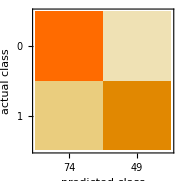
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 123
Accuracy | (91.12.6) %
Accuracy baseline | (56.4.) %
Geometric mean of probabilities | 0.614 ± 0.0083
Mean cross entropy | 0.488 ± 0.013
Single evaluation time | 3.73 ms/example
Batch evaluation speed | 980. examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[model,descriptor->outputs]
```

```mathematica
?Classify
```

```mathematica
MaxAbsEStateIndexdata=Table[descriptor[[i,"MaxAbsEStateIndex"]],{i,Length[descriptor]}]
```

{10.2621,5.96661,2.52958,5.12801,5.6185,12.0779,2.6089,12.4201,6.27581,10.3257,12.3869,13.8892,10.2652,12.1924,11.7264,5.49122,11.8348,11.8938,12.0555,12.4686,11.8621,11.8229,12.6308,11.7209,12.1214,5.20235,12.6345,4.70935,12.3188,12.5072,12.8439,4.39536,13.0246,10.0927,4.54142,11.5861,2.7,13.0037,8.92238,14.248,10.5823,11.5287,11.873,13.0764,4.26353,5.63105,10.527,5.66771,5.93486,5.4342,10.8909,12.1724,12.179,12.3188,11.622,12.4441,3.98357,8.86542,5.66632,12.9053,13.3417,12.464,5.59384,4.95679,11.6854,14.7938,10.4605,12.0257,12.1268,5.98358,12.1069,10.7746,11.9854,11.0886,11.7449,12.816,11.5805,12.7368,12.7707,10.6767,12.4153,11.236,12.5972,5.78669,13.25,14.102,9.53323,11.6918,5.44661,12.6448,12.453,9.7688,14.1105,11.0356,11.8519,11.022,12.735,5.8033,13.3985,4.40726,12.3663,9.48155,12.485,3.58894,11.016,12.8807,12.5805,10.9095,11.5686,13.6557,10.9779,9.21272,11.6551,11.9554,3.59556,12.1547,10.5481,12.3066,11.5258,8.53389,5.57921,12.7603,11.657}

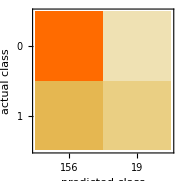
Classifier Measurements
Classifier method | RandomForest
Number of test examples | 175
Accuracy | (85.72.7) %
Accuracy baseline | (82.92.9) %
Geometric mean of probabilities | 0.605 ± 0.0078
Mean cross entropy | 0.502 ± 0.013
Single evaluation time | 3.82 ms/example
Batch evaluation speed | 1.09 examples/ms
-Graphics- |

```mathematica
testdata = Import ["https://raw.githubusercontent.com/zhu-research-group/auto_qsar_cl_transport/refs/tags/v1/ExternalTest.sdf","Metadata"];
smilesdatatest=Lookup["SMILES"]@testdata;
descriptortest=Values/@ features  /@ smilesdatatest;
outputstest = Lookup["Activity"]@testdata;


ClassifierMeasurements[model, descriptortest-> outputstest ]
```

```mathematica
descriptortest[[5]]
```

{4.4464,4.4464,0.761481,0.761481,0.73733,10.7222,238.294,224.182,238.122,90,0,0.142667,-0.36532,0.36532,0.142667,1.11111,1.94444,2.77778,15.0466,10.1988,2.05353,-2.07082,2.19025,-2.03086,5.8643,1.04574,2.84906,1.88212,657.871,12.372,10.143,10.143,8.8265,5.9229,5.9229,4.19853,4.19853,2.83029,2.83029,1.96944,1.96944,-2.36,26268.4,10.7726,4.4863,2.04554,105.098,10.3008,17.2894,0.,0.,0.,0.,0.,9.96796,0.,0.,30.3318,18.5536,12.7416,5.38622,0.,16.8513,0.,14.9519,0.,13.4685,5.31679,53.9829,0.,0.,5.31679,5.81786,0.,0.,14.9519,6.54476,6.92374,11.3879,42.595,0.,11.0334,0.,53.6,0.,0.,0.,0.,0.,29.2204,5.56345,0.,37.386,32.4015,0.,0.,0.,11.8989,4.38433,2.10696,1.64177,12.2617,1.88143,2.65828,0.,0.142857,18,2,4,0,0,0,0,1,2,3,0,0,3,2,4,2,3,0,0,0,0,0,2.68496,3,2.87842,72.3944,0,0,0,0,0,3,1,0,0,0,0,0,0,0,0,2,2,0,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}